## Physics 449 hw#6 Due 4/20 W12F

Name: Ruojun Wang
W12R 4/19

```mathematica
<<"http://www.physics.wisc.edu/~tgwalker/448defs.m"
```

Syntax::sntx: 
   Invalid syntax in or before 
    "<!DOCTYPE HTML PUBLIC "-//IETF//DTD HTML 2.0//EN">"
      ^
     (line 1 of
     "http://www.physics.wisc.edu/~tgwalker/448defs.m").

## 2) T 13.7

```mathematica
-μ/(2π ℏ^2)Integrate[Sin[θ] r^2 ⅇ^(-r/a)ⅇ^(ⅈ q r Cos[θ]),{r,0,∞},{θ,0,π},{ϕ,0,2π}]
```

ConditionalExpression[-(4 a^3 μ)/((1+a^2 q^2)^2 ℏ^2),Re[1/a]>Abs[Im[q]]]

## 5) Plot your results from 0 to 10eV, on a log scale. From your zero energy wavefunction, how many bound states are there in this potential?

It follows from the handout “SwaveScattering,”
		ⅆ_r^2 P+k^2 P=(2μ)/ℏ^2 V P
pick scaling length r=s Λ, and plug in V(r)=-V_0/(1+(r/b)^6)=(-9.5 eV)/(1+(r/(5 a_0))^6)
		ⅆ_s^2 P+(k Λ)^2 P=(2μ Λ^2)/ℏ^2 V_0/(1+((s Λ)/(5 a_0))^6) P

pick k_s=k Λ,Λ=a_0
		ⅆ_s^2 P+k_s^2 P=(2μ a_0^2)/ℏ^2 V_0/(1+(s/5)^6) P
		
With 1 E_h=ℏ^2/(m a_0)=27.2eV→ (2μ a_0^2)/ℏ^2 V_0/(1+(s/5)^6) P=2/27.2 9.5/(1+(s/5)^6) P

```mathematica
SE[ϵ_]:= -1/2 p''[s]-9.5/(27.2(1+(s/5)^5))p[s]==ϵ*p[s];
```

Calculate the scattering length: at large r 	P=A(s-a_s), P'=A→ a_s=s-P/P'

```mathematica
sm=40;p0[s_]=NDSolve[{SE[0],p[0]==0,p'[0]==1},p[s],{s,0,sm}]⟦1,1,2⟧
```

InterpolatingFunction[{{0., 40.}}, <>][s]

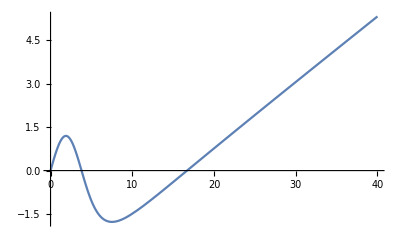

```mathematica
Plot[p0[s],{s,0,sm}]
```

```mathematica
sm-p0[sm]/p0'[sm]
```

16.407

```mathematica
σ0=4π %^2
```

3382.75

so the scattering length is a=16.407Λ and the cross section is σ=3382.75 Λ^2.  There are 3 bounded states b/c 3 crossings.

```mathematica
δ[k_]:=Module[{},pk[s_]=NDSolve[{k^2 p[s]+p''[s]==(2*9.5)/(27.2(1+(s/5)^6)) p[s],p[0]==0,p'[0]==1},p[s],{s,0,sm}]⟦1,1,2⟧;
Mod[ArcCot[pk'[sm]/(k pk[sm])]-k sm,π]]
```

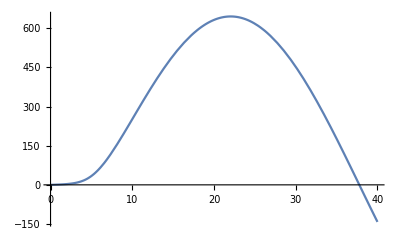

```mathematica
δ[.1];Plot[pk[s],{s,0,sm}]
```

```mathematica
ks=10^Range[-3,2,.03];
```

```mathematica
σs=Table[{k^2,Sin[δ[k]]^2(4π)/k^2},{k,ks}];
```

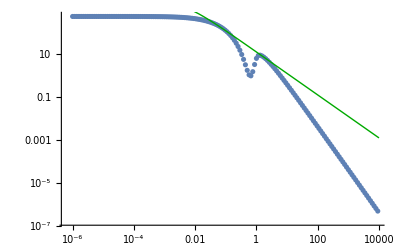

```mathematica
Show[ListLogLogPlot[σs],LogLogPlot[σ0/(1+σ0 ksq/(4π)),{ksq,.0001,10^4},PlotStyle->{Thick,Darker[Green]}]]
```